```mathematica
ClearAll[m1,m2]
Needs["PlotLegends`"]
mchirp[m1_,m2_]=(m1 m2)^(3/5) (m1+m2)^(-1/5);
f0=10;
myplotfn2[m1_,m2_,t_]= ((mchirp[m1,m2]*4.92549095*10^-6)*f0^9)^(1/8)(((mchirp[m1,m2]*4.92549095*10^-6)* f0)^(1/3)-256f0^3 (mchirp[m1,m2]*4.92549095*10^-6)^2N[π]^(8/3)(t/5))^(-3/8);
```

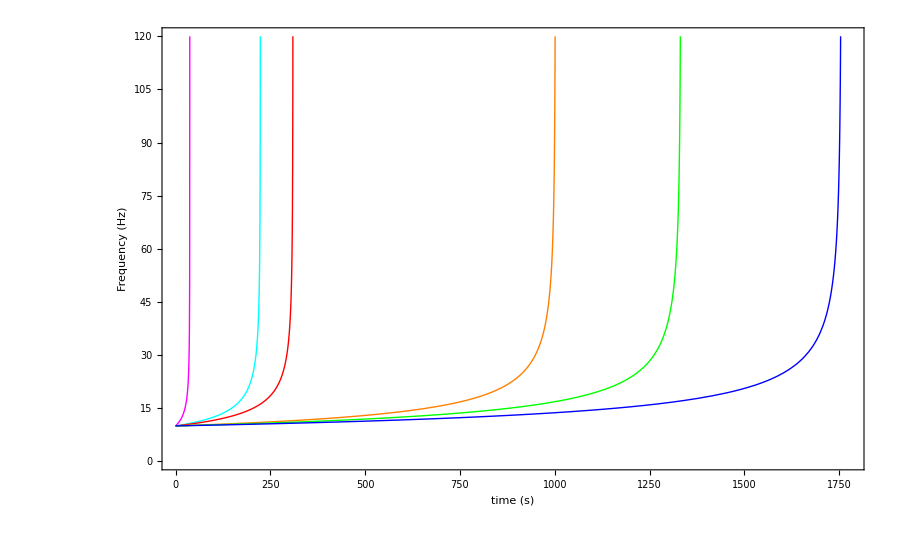

```mathematica
Needs["PlotLegends`"]
g2=Plot[{myplotfn2[10,10,t],myplotfn2[10,1.4,t],myplotfn2[10,1,t],myplotfn2[1.4,1.4,t],myplotfn2[1.4,1,t],myplotfn2[1,1,t]}
,{t,0,1780},PlotStyle->{{Thickness[Large],Magenta},{Thickness[Large],Cyan},{Thickness[Large],Red},{Thickness[Large],Orange},{Thickness[Large],Green},{Thickness[Large],Blue}},PlotRange->{{0,1780},{0,120}},Frame->True,ImageSize->900,PlotLegend->{Style["BH-BH",Bold,13],Style["BH-NS",Bold,13],Style["BH-WD",Bold,13],Style["NS-NS",Bold,13],Style["NS-WD",Bold,13],Style["WD-WD",Bold,13]},LegendPosition->{1,-0.25}, BaseStyle ->{FontFamily->"Arial",18},FrameLabel->{"time (s)","Frequency (Hz)"},LegendShadow->None]
```